## Definitions

```mathematica
GetEdgeTag[_(->)^tag__]:=tag
GetEdgeTag[_(<->)^tag__]:=tag
```

```mathematica
GetAllEdgeTags[g_Graph]:=Module[{},(
GetEdgeTag/@EdgeList[g]
)]
```

```mathematica
PruneSelfLoops[g_Graph]:=Module[{selfLoopEdgeTags,newg},(
selfLoopEdgeTags=Union[Cases[EdgeList[g],v_(->)^tag_ v_:>tag]];
newg=EdgeDelete[g,v_(->)^tag_ v_];
{newg,selfLoopEdgeTags}
)]
```

```mathematica
EdgeContractBugFixed[g_Graph,DirectedEdge[v1_,v2_,etag_]]:=Module[{newEdges,newVertices},
newEdges=Replace[Replace[#,DirectedEdge[v2,v_,tag_]:>DirectedEdge[v1,v,tag]],DirectedEdge[v_,v2,tag_]:>DirectedEdge[v,v1,tag]]&/@DeleteCases[EdgeList[g],DirectedEdge[v1,v2,etag]];(*Remove self-loops*)
newEdges=DeleteCases[newEdges,DirectedEdge[v_,v_,_]];
newVertices=DeleteCases[VertexList[g],v2];
Graph[newVertices,newEdges,Options[g]]
]
```

```mathematica
CFFReduce[g_Graph]:=Module[{selectedVertex,edgesToContract,allContractedGraphs,allTerms,Esurface,terms,edgeContractedGraph,EsurfacePlusOSE,EsurfaceMinusOSE,contractedOutEdges,contractedInEdges},
If[FreeQ[VertexDegree[g],a_/;a>0],
Return[{{}}];
];
selectedVertex=SelectFirst[VertexList[g],VertexDegree[g,#]>0&];
edgesToContract=EdgeList[g,DirectedEdge[selectedVertex,_,_]|DirectedEdge[_,selectedVertex,_]];
edgesToContract=GatherBy[edgesToContract,Replace[#,DirectedEdge[v1_,v2_,_]:>Sort[{v1,v2}]]&];
allContractedGraphs=Table[
edgeContractedGraph=EdgeContractBugFixed[g,multiedgeToContract[[1]]];
contractedOutEdges=Select[multiedgeToContract,MatchQ[DirectedEdge[selectedVertex,_,_]]];
contractedInEdges=Complement[multiedgeToContract,contractedOutEdges];
<|"ContractedOutEdges"->Sort[GetEdgeTag/@contractedOutEdges],"ContractedInEdges"->Sort[GetEdgeTag/@contractedInEdges],"Graph"->edgeContractedGraph|>
,
{multiedgeToContract,edgesToContract}
];
EsurfacePlusOSE=Sort[GetEdgeTag/@Select[Flatten[edgesToContract],MatchQ[DirectedEdge[selectedVertex,_,_]]]];
EsurfaceMinusOSE=Sort[GetEdgeTag/@Select[Flatten[edgesToContract],MatchQ[DirectedEdge[_,selectedVertex,_]]]];
allTerms=Table[
Esurface=<|"OverallFactor"->1,"PlusOSE"->EsurfacePlusOSE,"MinusOSE"->EsurfaceMinusOSE,"ContractedInEdges"->contractedGraph["ContractedInEdges"],"ContractedOutEdges"->contractedGraph["ContractedOutEdges"]|>;
terms=CFFReduce[contractedGraph["Graph"]];
Prepend[#,Esurface]&/@terms
,
{contractedGraph,allContractedGraphs}
];
Flatten[allTerms,1]
]
```

```mathematica
CFF[g_Graph]:=Module[{reducedGraph,selfLoopEdgeTags,allTerms},
(*Remove all unnecessary properties from the graph*)
reducedGraph=Graph[VertexList[g],EdgeList[g],VertexLabels->Automatic,EdgeLabels->"EdgeTag",GraphLayout->"TutteEmbedding"];
{reducedGraph,selfLoopEdgeTags}=PruneSelfLoops[reducedGraph];
allTerms=CFFReduce[reducedGraph];
allTerms=Table[<|"OverallFactor"->1,"ESurfaces"->term|>,{term,allTerms}];
allTerms
]
```

```mathematica
CFFToExpression[CFFterm_Association]:=Module[{overallFactor,ESurfaces,factors,result},
overallFactor=CFFterm["OverallFactor"];
ESurfaces=CFFterm["ESurfaces"];
ESurfaces=Table[
If[Length[ESurface["ContractedOutEdges"]]==1&&Length[ESurface["ContractedInEdges"]]==0,
ESurface["OverallFactor"]/(Total[e/@ESurface["PlusOSE"]]-Total[e/@ESurface["MinusOSE"]]),
If[Length[ESurface["ContractedInEdges"]]==1&&Length[ESurface["ContractedOutEdges"]]==0,
-ESurface["OverallFactor"]/(Total[e/@ESurface["PlusOSE"]]-Total[e/@ESurface["MinusOSE"]]),
ESurface["OverallFactor"](((Times@@(n[-1,e[#]]&/@ESurface["ContractedInEdges"]))(Times@@(n[1,e[#]]&/@ESurface["ContractedOutEdges"]))-(Times@@(n[1,e[#]]&/@ESurface["ContractedInEdges"]))(Times@@(n[-1,e[#]]&/@ESurface["ContractedOutEdges"])))/(Total[e/@ESurface["PlusOSE"]]-Total[e/@ESurface["MinusOSE"]]))
]
]
,
{ESurface,ESurfaces}
];
result=overallFactor Times@@ESurfaces;
result=result/.{e[tag_]:>σ[tag]e[tag]};
result
]
```

```mathematica
ZeroTLimit[expr_]:=Module[{result},
result=expr/.{n[s_,e_]:>s Θ[s e]};
result=result/.{Θ[a_ e[tag_]]:>Θ[a]};
result=result/.{Θ[σ[tag_]]:>1/2(1+σ[tag]),Θ[-σ[tag_]]:>1/2(1-σ[tag])};
result
]
```

```mathematica
GenerateOrientations[expr_,edgeTags_List]:=Module[{orientations},
orientations=Association[Thread[edgeTags->#]]&/@Tuples[{-1,1},Length[edgeTags]];
orientations=Table[
{orientation,expr/.{σ[tag_]:>orientation[tag]}}
,
{orientation,orientations}
];
orientations
]
```

## Examples

For simplicity, external legs are ignored.

### Double-triangle

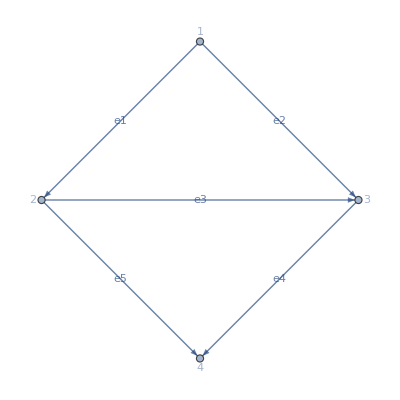

```mathematica
doubleTriangle=Graph[{1,2,3,4},{1(->)^("e1")2,1(->)^("e2")3,2(->)^("e3")3,3(->)^("e4")4,2(->)^("e5")4},VertexLabels->Automatic,EdgeLabels->"EdgeTag",GraphLayout->"TutteEmbedding"]
```

```mathematica
ttCFF=Total[CFFToExpression/@CFF[doubleTriangle]];
ttCFFZeroT=ZeroTLimit[ttCFF];
ttOrientations=GenerateOrientations[ttCFFZeroT,GetAllEdgeTags[doubleTriangle]];
```

The following is the single expression generating all orientations while keeping σ fully parametric. Note that Θ(σ_e) has been written as (1+σ_e)/2.

```mathematica
ttCFFZeroT
```

(-1/8 (1+σ[e2]) (1+σ[e3]) (1-σ[e4])-1/8 (1-σ[e2]) (1-σ[e3]) (1+σ[e4]))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e4] σ[e4]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]))+(1/8 (1+σ[e1]) (1-σ[e3]) (1-σ[e5])+1/8 (1-σ[e1]) (1+σ[e3]) (1+σ[e5]))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]-e[e5] σ[e5]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/4 (1-σ[e4]) (1-σ[e5])+1/4 (1+σ[e4]) (1+σ[e5])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e4] σ[e4]+e[e5] σ[e5]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (-1/4 (1-σ[e4]) (1-σ[e5])+1/4 (1+σ[e4]) (1+σ[e5])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]+e[e5] σ[e5]))

All orientations have been obtained by plugging in all possible σ values:

```mathematica
ttOrientations//MatrixForm
```

(<|e1→-1,e2→-1,e3→-1,e4→-1,e5→-1|> | 1/((-e[e1]-e[e2]) (-e[e2]-e[e3]-e[e5]) (-e[e4]-e[e5]))
<|e1→-1,e2→-1,e3→-1,e4→-1,e5→1|> | 0
<|e1→-1,e2→-1,e3→-1,e4→1,e5→-1|> | -1/((-e[e1]-e[e2]) (-e[e2]-e[e3]-e[e4]) (-e[e2]-e[e3]-e[e5]))
<|e1→-1,e2→-1,e3→-1,e4→1,e5→1|> | -1/((-e[e1]-e[e2]) (-e[e2]-e[e3]-e[e4]) (-e[e2]-e[e3]+e[e5]))-1/((-e[e1]-e[e2]) (-e[e2]-e[e3]+e[e5]) (e[e4]+e[e5]))
<|e1→-1,e2→-1,e3→1,e4→-1,e5→-1|> | -1/((-e[e1]-e[e2]) (-e[e1]-e[e3]-e[e4]) (-e[e4]-e[e5]))
<|e1→-1,e2→-1,e3→1,e4→-1,e5→1|> | 1/((-e[e1]-e[e2]) (-e[e1]-e[e3]-e[e4]) (-e[e1]-e[e3]-e[e5]))
<|e1→-1,e2→-1,e3→1,e4→1,e5→-1|> | 0
<|e1→-1,e2→-1,e3→1,e4→1,e5→1|> | 1/((-e[e1]-e[e2]) (-e[e1]-e[e3]+e[e4]) (-e[e1]-e[e3]-e[e5]))+1/((-e[e1]-e[e2]) (-e[e1]-e[e3]+e[e4]) (e[e4]+e[e5]))
<|e1→-1,e2→1,e3→-1,e4→-1,e5→-1|> | 0
<|e1→-1,e2→1,e3→-1,e4→-1,e5→1|> | 0
<|e1→-1,e2→1,e3→-1,e4→1,e5→-1|> | 0
<|e1→-1,e2→1,e3→-1,e4→1,e5→1|> | 0
<|e1→-1,e2→1,e3→1,e4→-1,e5→-1|> | -1/((-e[e1]+e[e2]) (e[e2]+e[e3]+e[e4]) (e[e2]+e[e3]-e[e5]))-1/((-e[e1]+e[e2]) (-e[e1]-e[e3]-e[e4]) (-e[e4]-e[e5]))-1/((-e[e1]+e[e2]) (e[e2]+e[e3]-e[e5]) (-e[e4]-e[e5]))
<|e1→-1,e2→1,e3→1,e4→-1,e5→1|> | 1/((-e[e1]+e[e2]) (-e[e1]-e[e3]-e[e4]) (-e[e1]-e[e3]-e[e5]))-1/((-e[e1]+e[e2]) (e[e2]+e[e3]+e[e4]) (e[e2]+e[e3]+e[e5]))
<|e1→-1,e2→1,e3→1,e4→1,e5→-1|> | 0
<|e1→-1,e2→1,e3→1,e4→1,e5→1|> | 1/((-e[e1]+e[e2]) (-e[e1]-e[e3]+e[e4]) (-e[e1]-e[e3]-e[e5]))+1/((-e[e1]+e[e2]) (-e[e1]-e[e3]+e[e4]) (e[e4]+e[e5]))+1/((-e[e1]+e[e2]) (e[e2]+e[e3]+e[e5]) (e[e4]+e[e5]))
<|e1→1,e2→-1,e3→-1,e4→-1,e5→-1|> | 1/((e[e1]-e[e2]) (e[e1]+e[e3]-e[e4]) (-e[e4]-e[e5]))+1/((e[e1]-e[e2]) (-e[e2]-e[e3]-e[e5]) (-e[e4]-e[e5]))+1/((e[e1]-e[e2]) (e[e1]+e[e3]-e[e4]) (e[e1]+e[e3]+e[e5]))
<|e1→1,e2→-1,e3→-1,e4→-1,e5→1|> | 0
<|e1→1,e2→-1,e3→-1,e4→1,e5→-1|> | -1/((e[e1]-e[e2]) (-e[e2]-e[e3]-e[e4]) (-e[e2]-e[e3]-e[e5]))+1/((e[e1]-e[e2]) (e[e1]+e[e3]+e[e4]) (e[e1]+e[e3]+e[e5]))
<|e1→1,e2→-1,e3→-1,e4→1,e5→1|> | -1/((e[e1]-e[e2]) (-e[e2]-e[e3]-e[e4]) (-e[e2]-e[e3]+e[e5]))-1/((e[e1]-e[e2]) (e[e1]+e[e3]+e[e4]) (e[e4]+e[e5]))-1/((e[e1]-e[e2]) (-e[e2]-e[e3]+e[e5]) (e[e4]+e[e5]))
<|e1→1,e2→-1,e3→1,e4→-1,e5→-1|> | 0
<|e1→1,e2→-1,e3→1,e4→-1,e5→1|> | 0
<|e1→1,e2→-1,e3→1,e4→1,e5→-1|> | 0
<|e1→1,e2→-1,e3→1,e4→1,e5→1|> | 0
<|e1→1,e2→1,e3→-1,e4→-1,e5→-1|> | 1/((e[e1]+e[e2]) (e[e1]+e[e3]-e[e4]) (-e[e4]-e[e5]))+1/((e[e1]+e[e2]) (e[e1]+e[e3]-e[e4]) (e[e1]+e[e3]+e[e5]))
<|e1→1,e2→1,e3→-1,e4→-1,e5→1|> | 0
<|e1→1,e2→1,e3→-1,e4→1,e5→-1|> | 1/((e[e1]+e[e2]) (e[e1]+e[e3]+e[e4]) (e[e1]+e[e3]+e[e5]))
<|e1→1,e2→1,e3→-1,e4→1,e5→1|> | -1/((e[e1]+e[e2]) (e[e1]+e[e3]+e[e4]) (e[e4]+e[e5]))
<|e1→1,e2→1,e3→1,e4→-1,e5→-1|> | -1/((e[e1]+e[e2]) (e[e2]+e[e3]+e[e4]) (e[e2]+e[e3]-e[e5]))-1/((e[e1]+e[e2]) (e[e2]+e[e3]-e[e5]) (-e[e4]-e[e5]))
<|e1→1,e2→1,e3→1,e4→-1,e5→1|> | -1/((e[e1]+e[e2]) (e[e2]+e[e3]+e[e4]) (e[e2]+e[e3]+e[e5]))
<|e1→1,e2→1,e3→1,e4→1,e5→-1|> | 0
<|e1→1,e2→1,e3→1,e4→1,e5→1|> | 1/((e[e1]+e[e2]) (e[e2]+e[e3]+e[e5]) (e[e4]+e[e5])))

Cancellations of H-surfaces occur in the following way:

```mathematica
ttOrientations[[4,2]]
%//Simplify
```

-1/((-e[e1]-e[e2]) (-e[e2]-e[e3]-e[e4]) (-e[e2]-e[e3]+e[e5]))-1/((-e[e1]-e[e2]) (-e[e2]-e[e3]+e[e5]) (e[e4]+e[e5]))

-1/((e[e1]+e[e2]) (e[e2]+e[e3]+e[e4]) (e[e4]+e[e5]))

### Triangle-box-triangle

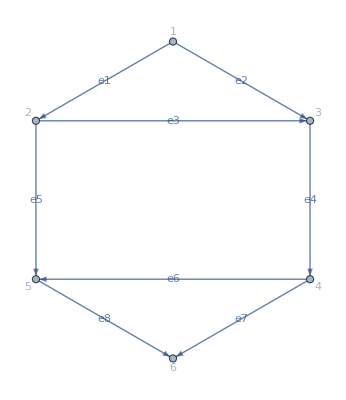

```mathematica
triangleBoxTriangle=Graph[{1,2,3,4,5,6},{1(->)^("e1")2,1(->)^("e2")3,2(->)^("e3")3,3(->)^("e4")4,2(->)^("e5")5,4(->)^("e6")5,4(->)^("e7")6,5(->)^("e8")6},VertexLabels->Automatic,EdgeLabels->"EdgeTag",GraphLayout->"TutteEmbedding"]
```

```mathematica
tbtCFF=Total[CFFToExpression/@CFF[triangleBoxTriangle]];
tbtCFFZeroT=ZeroTLimit[tbtCFF];
tbtOrientations=GenerateOrientations[tbtCFFZeroT,GetAllEdgeTags[triangleBoxTriangle]];
```

```mathematica
tbtCFFZeroT
```

((1/8 (1+σ[e2]) (1+σ[e3]) (1-σ[e4])+1/8 (1-σ[e2]) (1-σ[e3]) (1+σ[e4])) (1/4 (1-σ[e6]) (1-σ[e7])-1/4 (1+σ[e6]) (1+σ[e7])))/((e[e1] σ[e1]+e[e2] σ[e2]) (-e[e2] σ[e2]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (1/8 (1+σ[e4]) (1-σ[e6]) (1-σ[e7])+1/8 (1-σ[e4]) (1+σ[e6]) (1+σ[e7])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e4] σ[e4]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]+e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (1/8 (1+σ[e4]) (1-σ[e6]) (1-σ[e7])+1/8 (1-σ[e4]) (1+σ[e6]) (1+σ[e7])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e4] σ[e4]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (1/8 (1+σ[e4]) (1-σ[e6]) (1-σ[e7])+1/8 (1-σ[e4]) (1+σ[e6]) (1+σ[e7])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e4] σ[e4]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (1/8 (1+σ[e4]) (1-σ[e6]) (1-σ[e7])+1/8 (1-σ[e4]) (1+σ[e6]) (1+σ[e7])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]-e[e6] σ[e6]-e[e7] σ[e7]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]))+((1/8 (1+σ[e1]) (1-σ[e3]) (1-σ[e5])+1/8 (1-σ[e1]) (1+σ[e3]) (1+σ[e5])) (-1/4 (1+σ[e6]) (1-σ[e8])+1/4 (1-σ[e6]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]-e[e5] σ[e5]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]-e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/8 (1+σ[e5]) (1+σ[e6]) (1-σ[e8])-1/8 (1-σ[e5]) (1-σ[e6]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e5] σ[e5]+e[e6] σ[e6]-e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (-1/8 (1+σ[e5]) (1+σ[e6]) (1-σ[e8])-1/8 (1-σ[e5]) (1-σ[e6]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e5] σ[e5]+e[e6] σ[e6]-e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/8 (1+σ[e5]) (1+σ[e6]) (1-σ[e8])-1/8 (1-σ[e5]) (1-σ[e6]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e5] σ[e5]+e[e6] σ[e6]-e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/8 (1+σ[e5]) (1+σ[e6]) (1-σ[e8])-1/8 (1-σ[e5]) (1-σ[e6]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]-e[e8] σ[e8]) (e[e5] σ[e5]+e[e6] σ[e6]-e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/4 (1-σ[e5]) (1-σ[e6])+1/4 (1+σ[e5]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e7] σ[e7]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (-1/4 (1-σ[e5]) (1-σ[e6])+1/4 (1+σ[e5]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e7] σ[e7]+e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/4 (1-σ[e5]) (1-σ[e6])+1/4 (1+σ[e5]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e5] σ[e5]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e7] σ[e7]+e[e8] σ[e8]))-((1/8 (1+σ[e2]) (1+σ[e3]) (1-σ[e4])+1/8 (1-σ[e2]) (1-σ[e3]) (1+σ[e4])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (-e[e2] σ[e2]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e7] σ[e7]+e[e8] σ[e8]))+((-1/4 (1+σ[e1]) (1-σ[e3])+1/4 (1-σ[e1]) (1+σ[e3])) (-1/4 (1+σ[e4]) (1-σ[e6])+1/4 (1-σ[e4]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e7] σ[e7]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (-1/4 (1+σ[e4]) (1-σ[e6])+1/4 (1-σ[e4]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e4] σ[e4]+e[e5] σ[e5]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e7] σ[e7]+e[e8] σ[e8]))+((-1/4 (1-σ[e2]) (1-σ[e3])+1/4 (1+σ[e2]) (1+σ[e3])) (-1/4 (1+σ[e4]) (1-σ[e6])+1/4 (1-σ[e4]) (1+σ[e6])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e2] σ[e2]+e[e3] σ[e3]+e[e5] σ[e5]) (e[e2] σ[e2]+e[e3] σ[e3]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e4] σ[e4]-e[e6] σ[e6]+e[e8] σ[e8]) (e[e7] σ[e7]+e[e8] σ[e8]))+((1/8 (1+σ[e1]) (1-σ[e3]) (1-σ[e5])+1/8 (1-σ[e1]) (1+σ[e3]) (1+σ[e5])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]-e[e5] σ[e5]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e1] σ[e1]-e[e3] σ[e3]-e[e5] σ[e5]+e[e7] σ[e7]+e[e8] σ[e8]))+((1/8 (1+σ[e1]) (1-σ[e3]) (1-σ[e5])+1/8 (1-σ[e1]) (1+σ[e3]) (1+σ[e5])) (-1/4 (1-σ[e7]) (1-σ[e8])+1/4 (1+σ[e7]) (1+σ[e8])))/((e[e1] σ[e1]+e[e2] σ[e2]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e4] σ[e4]) (e[e1] σ[e1]-e[e3] σ[e3]+e[e6] σ[e6]+e[e7] σ[e7]) (e[e7] σ[e7]+e[e8] σ[e8]) (e[e1] σ[e1]-e[e3] σ[e3]-e[e5] σ[e5]+e[e7] σ[e7]+e[e8] σ[e8]))

```mathematica
ToExpression[StringTake["e1234",2;;-1]]
```

1234

```mathematica
tbtOrientations
```

```mathematica
tbtOrientations[[1]]⟦1⟧
```

<|e1→-1,e2→-1,e3→-1,e4→-1,e5→-1,e6→-1,e7→-1,e8→-1|>

```mathematica
tbtOrientations⟦1⟧⟦1⟧
```

<|e1→-1,e2→-1,e3→-1,e4→-1,e5→-1,e6→-1,e7→-1,e8→-1|>

```mathematica
Triangle-box-triangle
```

-box-triangle+Triangle

### Triangle-box-triangle with CFF

#### resources

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/"<>"cLTD.m"];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

```mathematica
FORMPATH="form";(*"<PASTE_HERE_YOUR_FULL_FORM_PATH_HERE_INSTEAD>"*)
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->"./",
	"FORMpath"->"form",
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→form
tFORMpath→tform
WorkingDirectory→./
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

#### triangle-box-triangle evaluation

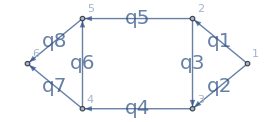

```mathematica
tBt=Graph[{1,2,3,4,5,6},{1->2,1->3,2->3,3->4,2->5,4->5,4->6,5->6},VertexLabels->Automatic,EdgeLabels->Automatic];
tBt=AssignSignatures[tBt,masses-><|1->1,2->2,3->3,4->4,5->5,6->6|>,lmb->{1,5,8}];
tBt=DirectedGraph[tBt,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[tBt]}]]
```

```mathematica
tBtnumerics=GenerateRandomSample[tBt,Seed->1]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},k3→{17/19,19/23,23/29}}

```mathematica
tBtCFF=CrossFreeFamilyLTD[tBt,ConvertToNormalisedFormat->True];
```

```mathematica
Print["cFF result : ",EvalcFF[tBt,tBtCFF,tBtnumerics,Num->1,DEBUG->False]//N//FullForm];
```

cFF result : Complex[0.,1.1749×10^-8]

```mathematica
tLTDResMappedConventions=Table[{Association[SortBy[Table[ToExpression[StringTake[oi,2;;-1]]->res⟦1⟧[oi],{oi,Keys[res⟦1⟧]}],#⟦1⟧&]],(res[[2]]//.Table[e["e"<>ToString[i]]->OSE[i],{i,1,8}])},{res,tbtOrientations}];
```

```mathematica
OSEReplacements=ComputeOSEReplacements[tBt,tBtnumerics];
```

```mathematica
resdLTD=Association[Table[{
o⟦1⟧->(((1/(Times@@Table[2*OSE[i],{i,1,8}]))*o⟦2⟧)/.OSEReplacements)
},{o,tLTDResMappedConventions}]];
```

```mathematica
resCFF=Association[Table[{
Association[SortBy[Table[oi->o["Orientation"][oi],{oi,Keys[o["Orientation"]]}],#⟦1⟧&]]-> EvalcFF[tBt,{o},tBtnumerics,Num->1,DEBUG->False]
},{o,tBtCFF}]];
```

```mathematica
dLTDOrientations=Keys[resdLTD];
```

```mathematica
CFFOrientations=Keys[resCFF];
```

```mathematica
CFFOrientations⟦1⟧
```

<|1→-1,2→-1,3→-1,4→-1,5→-1,6→-1,7→-1,8→-1|>

```mathematica
dLTDOrientations⟦1⟧
```

<|1→-1,2→-1,3→-1,4→-1,5→-1,6→-1,7→-1,8→-1|>

```mathematica
SymmetricDifference[dLTDOrientations,CFFOrientations]//Length
Complement[dLTDOrientations,CFFOrientations]//Length
Complement[CFFOrientations,dLTDOrientations]//Length
```

130

130

0

```mathematica
KeyExistsQ[<|"a"->2|>,"a"]
```

True

```mathematica
Block[{res, totdLTD=0, totCFF=0},
res=Table[
Block[{rdLTD,rCFF,diffPerc,avg,nPlus},
nPlus=Total[Table[If[o[oi]>0,1,0],{oi,Keys[o]}]];
rdLTD=resdLTD[o];
rCFF= (-1)^nPlus(-ⅈ) If[KeyExistsQ[resCFF,o],resCFF[o],0];
totdLTD=totdLTD+rdLTD;
totCFF=totCFF+rCFF;
avg = (Abs[rdLTD]+Abs[rCFF])/2;
diffPerc=If [avg===0, Abs[N[rdLTD]-N[rCFF]],Abs[N[rdLTD]-N[rCFF]]/avg]*100.;
{
StringJoin[Table[If[o[oi]>0,"+","-"],{oi,Keys[o]}]],
rdLTD//N//FullForm,
rCFF//N//FullForm,
diffPerc
}
],{o,Keys[resdLTD]}];
Print["Total dLTD: ",totdLTD//N//FullForm];
Print["Total CFF : ",totCFF//N//FullForm];
res//Dataset
]
```

Total dLTD: -9.08066×10^-10

Total CFF : -9.08066×10^-10